```mathematica
Φ[x_,y_]=-1/(√(x^2+y^2));
ForceDiscrete[x_,y_]:=-{(Φ[Floor[x+1],Floor[y]]-Φ[Floor[x],Floor[y]])(1-(y-Floor[y]))+(y-Floor[y])(Φ[Floor[x+1],Floor[y+1]]-Φ[Floor[x],Floor[y+1]]),(Φ[Floor[x],Floor[y+1]]-Φ[Floor[x],Floor[y]])(1-(x-Floor[x]))+(x-Floor[x]) (Φ[Floor[x+1],Floor[y+1]]-Φ[Floor[x+1],Floor[y]])};
```

```mathematica
RealForce[x,y]:={D[Φ[x,y],x],D[Φ[x,y],y]}
```

```mathematica
a=10
```

10

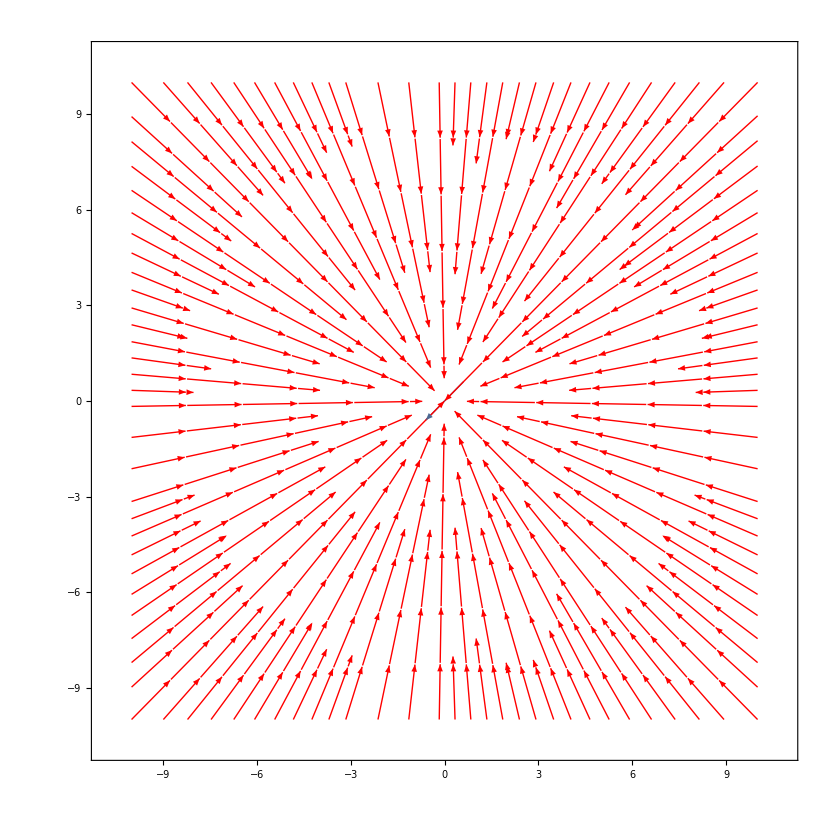

```mathematica
VectorPlot[({-x/((x^2+y^2)^(3/2)),-y/((x^2+y^2)^(3/2))}),{x,a,-a},{y,a,-a},
StreamPoints->Fine,PerformanceGoal->"Quality",StreamColorFunction->Hue,VectorPoints->Fine,VectorScale->Small]
```

```mathematica
RealForce[x,y]
```

RealForce[x,y]

```mathematica
RealForce[x,y]/.{x->1,y->1}
```

{1/(2 √2),1/(2 √2)}

```mathematica
(*ForceDiscrete[x,y]-RealForce[x,y]*)
```

```mathematica
(ForceDiscrete[x,y]-RealForce[x,y])/RealForce[x,y];a=10
```

10

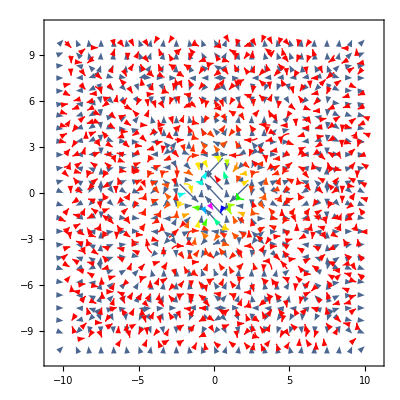

```mathematica
VectorPlot[(ForceDiscrete[x,y]+{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))}),{x,a,-a},{y,a,-a},
StreamPoints->Fine,PerformanceGoal->"Quality",StreamColorFunction->Hue,VectorPoints->Fine,VectorScale->Small]
```

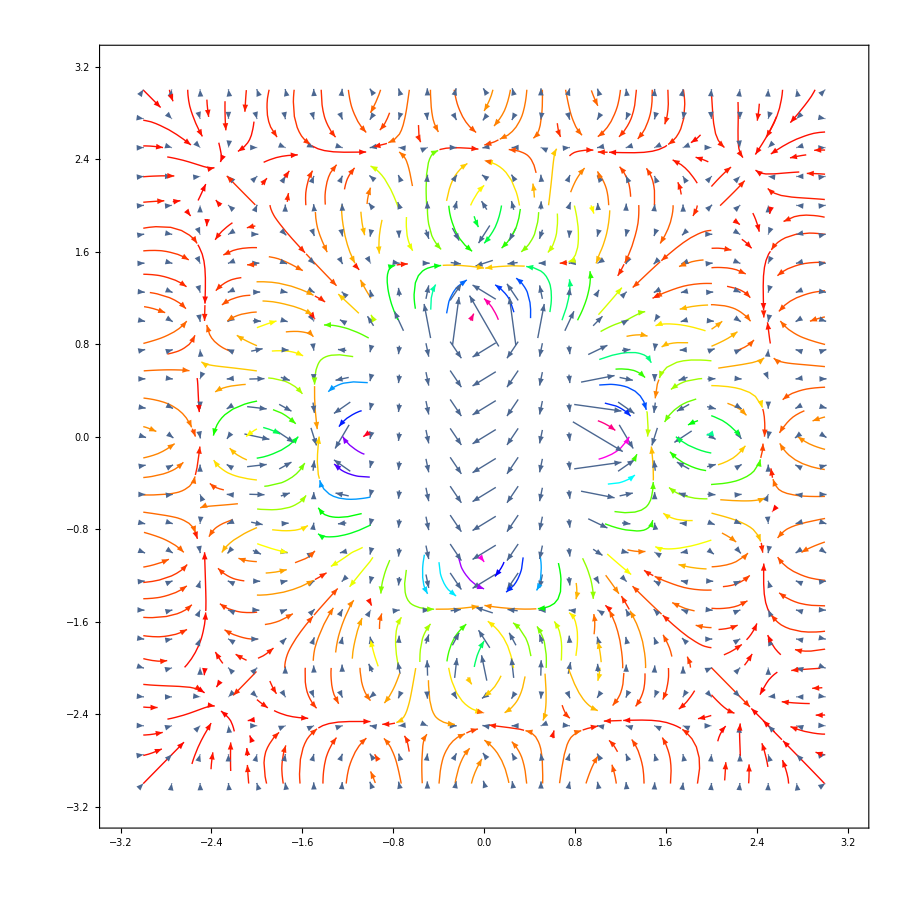

```mathematica
dx=10^-3
```

1/1000

```mathematica
AnalyticFx[x_,y_]:=-((x(1+0 dx-dx/2))/((√(x^2+y^2))^3)+dx/((√(x^2+y^2))^5)(3/2 x^2+3x y))
AnalyticFy[x_,y_]:=-((y(1+0dx-dx/2))/((√(x^2+y^2))^3)+dx/((√(x^2+y^2))^5)(3/2 y^2+3x y))
```

```mathematica
{AnalyticFx[x,y]+x/((x^2+y^2)^(3/2)),AnalyticFy[x,y]+y/((x^2+y^2)^(3/2))}/RealForce[x,y]/.{x->10,y->10}//N
```

{0.000275,0.000275}

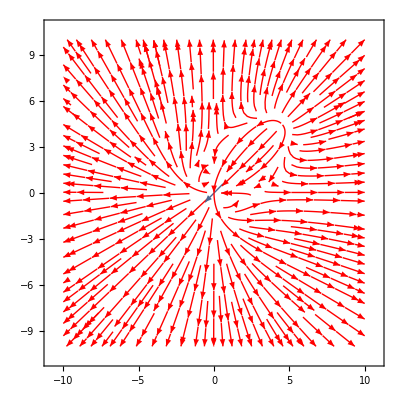

```mathematica
VectorPlot[({AnalyticFx[x,y]+x/((x^2+y^2)^(3/2)),AnalyticFy[x,y]+y/((x^2+y^2)^(3/2))}/100),{x,a,-a},{y,a,-a},
StreamPoints->Fine,PerformanceGoal->"Quality",StreamColorFunction->Hue,VectorPoints->Fine,VectorScale->Small]
```

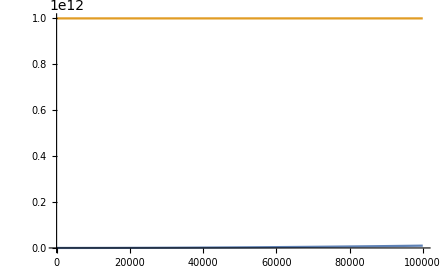

```mathematica
Plot[{N^2,10^12},{N,10,10^5}]
```